```mathematica
Needs["CUDALink`"]
CUDAQ[]
```

True

```mathematica
generateentire[]:=Block[{NLines,c1,th,LL,lines,LINES,NCircles,CIRCS,disks,rx,ry},
NLines=RandomInteger[{7,16}];
LINES=Table[
c1={RandomReal[{-5,5}],RandomReal[{-5,5}]};
th=RandomReal[{0,2π}];
LL=RandomReal[{0,5}];
lines={Thickness[RandomReal[{0.003,0.005}]],Line[{c1,c1+LL{Cos[th],Sin[th]}}]}
,{NLines}];
NCircles=RandomInteger[{7,16}];
CIRCS=Table[
c1={RandomReal[{-5,5}],RandomReal[{-5,5}]};
rx=RandomReal[{0.25,0.5}];
ry=RandomReal[{0.25,0.5}];
disks=Disk[c1,{rx,ry}]
,{NCircles}];
Graphics[{LINES,CIRCS},PlotRange->{{-5,5},{-5,5}}]
]
generateline[]:=Block[{NLines,c1,th,LL,thi,lines1,lines2,BOX},
c1={0,0};
BOX=RandomReal[{0.5,1.5}];
th=RandomReal[{0,2π}];
LL=RandomReal[{0,1}];
thi=RandomReal[{0.001,0.08}];
lines1={Thickness[thi],Line[{c1,c1+LL{Cos[th],Sin[th]}}]};
lines2={Thickness[thi],Line[{c1,c1-LL{Cos[th],Sin[th]}}]};
Graphics[{lines1,lines2},PlotRange->{{-BOX,BOX},{-BOX,BOX}},ImageSize->{128,128}]
]
```

```mathematica
generatecirc[]:=Block[{NLines,c1,th,LL,lines,LINES,NCircles,CIRCS,disks,rx,ry,BOX},
c1={0,0};
BOX=RandomReal[{0.5,1.5}];
rx=RandomReal[{0.25,0.5}];
ry=RandomReal[{0.25,0.5}];
disks=Disk[c1,{rx,ry}];
Graphics[disks,PlotRange->{{-BOX,BOX},{-BOX,BOX}},ImageSize->{128,128}]
]
```

```mathematica
generateblank[]:=Block[{NLines,c1,th,LL,lines,LINES,NCircles,CIRCS,disks,rx,ry,BOX,rrr,thi,lines1,lines2},
rrr=RandomReal[];
If[rrr<0.6,
Graphics[{White,Disk[]},PlotRange->{{-1,1},{-1,1}},ImageSize->{128,128}],
If[rrr<0.8,
BOX=RandomReal[{0.5,1.5}];
c1={RandomReal[{-BOX,BOX}],RandomReal[{-BOX,BOX}]};
rx=RandomReal[{0.25,0.5}];
ry=RandomReal[{0.25,0.5}];
disks=Disk[c1,{rx,ry}];
Graphics[disks,PlotRange->{{-BOX,BOX},{-BOX,BOX}},ImageSize->{128,128}]
,
BOX=RandomReal[{0.5,1
.5}];
c1={RandomReal[{-BOX,BOX}],RandomReal[{-BOX,BOX}]};
th=RandomReal[{0,2π}];
LL=RandomReal[{0,1}];
thi=RandomReal[{0.01,0.03}];
lines1={Thickness[thi],Line[{c1,c1+LL{Cos[th],Sin[th]}}]};
lines2={Thickness[thi],Line[{c1,c1-LL{Cos[th],Sin[th]}}]};
Graphics[{lines1,lines2},PlotRange->{{-BOX,BOX},{-BOX,BOX}},ImageSize->{128,128}]
]
]
]
```

```mathematica
lines = Table[generateline[]->1,{8000}];
circs = Table[generatecirc[]-> 2,{8000}];
blanks = Table[generateblank[]-> 3,{8000}];
data = Join[lines, circs, blanks];
data = RandomSample[data];
Length[data]
```

24000

```mathematica
training=data[[1;;20000]];
test=data[[20001;;]];
```

```mathematica
network=NetChain[{ConvolutionLayer[170,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],FlattenLayer[],100,DropoutLayer[],Ramp,3,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{1,2,3}}],"Input"->NetEncoder[{"Image",{128,128},"Grayscale"}]]
```

NetChain[<>]

```mathematica
network2=NetChain[{ConvolutionLayer[16,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],ConvolutionLayer[32,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],ConvolutionLayer[64,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],FlattenLayer[],100,DropoutLayer[],Ramp,3,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{1,2,3}}],"Input"->NetEncoder[{"Image",{128,128},"Grayscale"}]]
```

NetChain[<>]

```mathematica
network2=NetChain[{ConvolutionLayer[8,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],ConvolutionLayer[16,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],ConvolutionLayer[32,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],ConvolutionLayer[64,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],FlattenLayer[],100,DropoutLayer[],Ramp,3,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{1,2,3}}],"Input"->NetEncoder[{"Image",{128,128},"Grayscale"}]]
```

NetChain[<>]

```mathematica
window=100;
stepsize=2500;
counter = 0;
minloss=2345346546565556;
```

```mathematica
net=NetTrain[network,training,ValidationSet->test,MaxTrainingRounds->300];
```

```mathematica
net2=NetTrain[network2,training,ValidationSet->test,MaxTrainingRounds->1000,TargetDevice->"GPU", TrainingProgressFunction->{If[#BatchLoss<2345346546565556(*minloss*),minloss=#BatchLoss;
Print[#BatchLoss,"   ",#Round];
counter++;
Export["/scratch/classify_net_"<>ToString[counter]<>".wlnet",#Net]]&,"Interval"->Quantity[stepsize,"Batches"]}]
```

NetChain[<>]

```mathematica
net2[test[[1]][[1]],"Probabilities"]
```

<|1→4.9831×10^-7,2→0.998487,3→0.001513|>

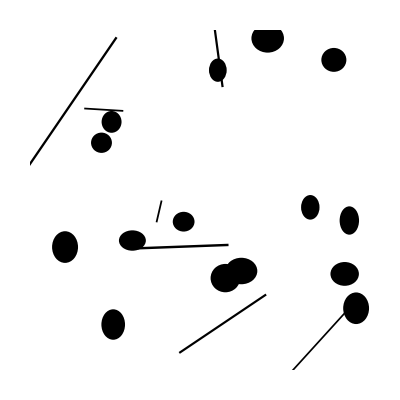

```mathematica
image=generateentire[]
```

```mathematica
imagedata=ImageData[ColorConvert[image,"Grayscale"]];
```

```mathematica
imagedata=1-imagedata;
```

```mathematica
imagedata=ArrayPad[imagedata,64];
```

```mathematica
Dimensions[imagedata]
```

{488,488}

```mathematica
i=333
j=333
```

333

333

```mathematica
net2[ArrayPlot[imagedata[[i-30;;i+20,j-20;;j+20]],PlotRangePadding->None,Frame->False,ImageSize->{128,128}],"Probabilities"]
```

<|1→3.53548×10^-11,2→6.89875×10^-12,3→1.|>

```mathematica
DistributeDefinitions[net2];
ps=Table[
Print[i];
Table[
p=net2[ArrayPlot[imagedata[[i-30;;i+30,j-30;;j+30]],PlotRangePadding->None,Frame->False,ImageSize->{128,128}],"Probabilities"];
{p[1],p[2],p[3]}
,{j,64,488-64,2}]
,{i,64,488-64,2}];
```

```mathematica
cmap=(Blend[{{0,Blue},{0.25,Green},{0.5,Yellow},{0.75,Orange},{1,Red}},#]&);
```

```mathematica
ImageAssemble[{ArrayPlot[ps[[All,All,1]],ColorFunction->cmap,PlotRangePadding->None]
,ArrayPlot[ps[[All,All,2]],ColorFunction->cmap,PlotRangePadding->None]
,ArrayPlot[ps[[All,All,3]],ColorFunction->cmap,PlotRangePadding->None]
}]
```

-Graphics-

```mathematica
{
```

```mathematica
ArrayPlot[imagedata]
```

-Graphics-

```mathematica
cm=ClassifierMeasurements[net2,test[[1;;500]]]
```

ClassifierMeasurementsObject[…]

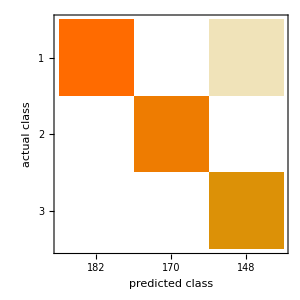

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["WorstClassifiedExamples"->2]
```

{-Graphics-→1,-Graphics-→1}